```mathematica
g = 9.8;
A = 0.5;
p = 1.2;
CC = 1.2
m = 90;
v[t_]:=Sqrt[2*g*m/(A*CC*p)]*Tanh[t*Sqrt[A*CC*p*g/(2*m)]];
```

1.2

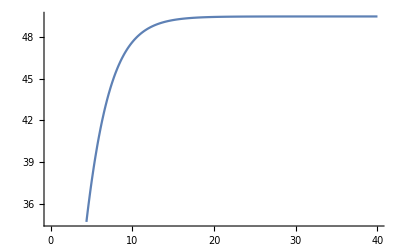

```mathematica
Plot[v[t], {t, 0, 40}]
```

```mathematica
Integrate[v[t], t]
```

250. Log[Cosh[0.19799 t]]

```mathematica
x[t_] := 250*Log[Cosh[0.19799t]]
```

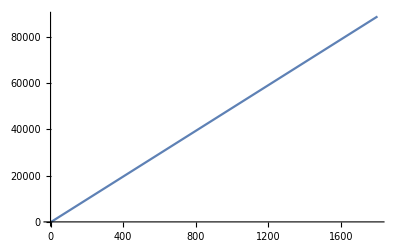

```mathematica
Plot[x[t], {t, 0, 1800}]
```

```mathematica
Solve[x[t] == 39000, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-791.42},{t→791.42}}